# Final Exam

Note: If you get to a part where you know exactly what you need to do but don’t know how to make Mathematica do it, please write clearly and explicitly what you would do. We will give you at least partial credit for correct reasoning even if the code doesn’t quite work. (But do your best to get the code to work! All Mathematica techniques you will need for this exam you have already seen in some form in the homework.)

## Problem 12

A charged particle of mass m = 0.03 kg and charge q = 0.2×10^-6C is constrained to move along the x axis. A second charged particle with Q = -1×10^-6 C is fixed in place at a position (x, y) = (0, 0.05 m). Calculate the period of oscillation if the charge q is released from rest at a position x = – 0.1255 m. The nearest tenth of a second is sufficient. Note that the potential energy between two charges is U = k q_1 q_2  / r, where k = 8.99 ×10^9 N m^2/C^2. 
-Graphics-

```mathematica
Quit[]
Clear["`*"]
```

```mathematica
k=8.99*10^9;

Q=-1*10^-6;
r1={-.1255,0};
r2={0,0.05};

q=0.2*10^-6;
r={x[t],y[t]}; (* we use the function notation so we can solve the differential equations later *)
m=0.03;
```

```mathematica
U =k*Q*q*(1/Norm[r-r1]+1/Norm[r-r2]);
U=ComplexExpand[U]
```

(0.+0. ⅈ)-0.001798/(√(x[t]^2+(-0.05+y[t])^2))-0.001798/(√((0.1255+x[t])^2+y[t]^2))

```mathematica
F=-Grad[U,{x[t],y[t]}]
```

{-(0.001798 x[t])/((x[t]^2+(-0.05+y[t])^2)^(3/2))-(0.001798 (0.1255+x[t]))/(((0.1255+x[t])^2+y[t]^2)^(3/2)),-(0.001798 (-0.05+y[t]))/((x[t]^2+(-0.05+y[t])^2)^(3/2))-(0.001798 y[t])/(((0.1255+x[t])^2+y[t]^2)^(3/2))}

-(0.001798 x[t])/((x[t]^2+(-0.05+y[t])^2)^(3/2))-(0.001798 (0.1255+x[t]))/(((0.1255+x[t])^2+y[t]^2)^(3/2))==0.03 x''[t]

-(0.001798 (-0.05+y[t]))/((x[t]^2+(-0.05+y[t])^2)^(3/2))-(0.001798 y[t])/(((0.1255+x[t])^2+y[t]^2)^(3/2))==0.03 y''[t]

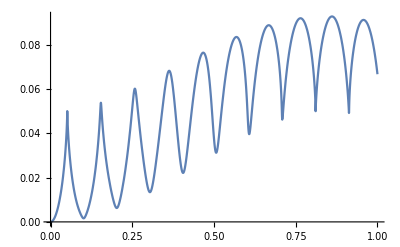

```mathematica
eqx = F[[1]]==m*x''[t]
eqy = F[[2]]==m*y''[t]
x0=0;
vx0=0;
y0=0;
vy0=0;
sol1=NDSolve[{eqx,eqy,x[0]==x0,y[0]==y0,x'[0]==vx0,y'[0]==vy0},{x,y},{t,0,1}];
Plot[{Sqrt[x[t]^2+y[t]^2]}/.sol1,{t,0,1}]
```

The period of oscillation is: 0.1 s

```mathematica
(* The rest of this is other work I did on this problem *)
```

```mathematica
k=8.99*10^9;
m=0.03;
q=0.2*10^-6;
Q=-1*10^-6;

x0=-.1255;
y0=0.05;
r0=Sqrt[x0^2+y0^2]
```

0.135093

```mathematica
Ur=k*q*Q/(x^2+y^2)
```

-0.001798/(x^2+y^2)

```mathematica
Fr=-D[Ur,x]-D[Ur,y]
```

-(0.003596 x)/((x^2+y^2)^2)-(0.003596 y)/((x^2+y^2)^2)

```mathematica
rule={x->x[t],y->y[t]};
```

```mathematica
xeq=m*x''[t]==Fr
yeq=m*y''[t]==-0.001798/y[t]^2
```

0.03 x''[t]==-0.001798/x[t]^2

0.03 y''[t]==-0.001798/y[t]^2

```mathematica
solx=NDSolve[{xeq,x[0]==x0,x'[0]==0},x,{t,0,10}]
soly=NDSolve[{yeq,y[0]==y0,y'[0]==0},y,{t,0,10}]
```

{{x→InterpolatingFunction[…]}}

NDSolve::ndsz: At t == 0.0507254, step size is effectively zero; singularity or stiff system suspected.

{{y→InterpolatingFunction[…]}}

```mathematica
r[t]=solx+soly;
```

```mathematica
Plot[r[t],{t,0,5}]
```

-Graphics-

```mathematica
k=8.99*10^9;
m=0.03;
q=0.2*10^-6;
Q=-1*10^-6;
xq0=-.1255;
yq0=0;
xQ0=0;
yQ0=0.05;

rq0={-.1255,0}
rQ0={0,0.05};
r=rq0-rQ0;
x=Norm[r]*Cos[theta];
y=Norm[r]*Sin[theta];
```

{-0.1255,0}

```mathematica
r=Sqrt[x^2+y^2]
U=k*q*Q/r
T=1/2*m*thetadot^2
L=T-U
```

√(0.0182503 Cos[theta]^2+0.0182503 Sin[theta]^2)

-0.001798/(√(0.0182503 Cos[theta]^2+0.0182503 Sin[theta]^2))

0.015 thetadot^2

0.015 thetadot^2+0.001798/(√(0.0182503 Cos[theta]^2+0.0182503 Sin[theta]^2))

```mathematica
rule={theta->theta[t],thetadot->theta'[t]};
dLdtheta=D[L,theta]/.rule
dLdthetadot = D[L,thetadot]/.rule

eqtheta=dLdtheta==D[dLdthetadot,t]
```

0.

0.03 theta'[t]

0.==0.03 theta''[t]

```mathematica
sol1=NDSolve[{eqtheta,x[0]==xq0,y[0]==yq0,x'[0]==0,y'[0]==0},{x,y},{t,0,10}];
Plot[{x[t],y[t]}/.sol1,{t,0,10}]
```

NDSolve::dvnoarg: The function theta appears with no arguments.

NDSolve::dsvar: 0.000204286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{0.==0.03 theta''[0.000204286],(0.135093 Cos[theta])[0]==-0.1255,(0.135093 Sin[theta])[0]==0,(0.135093 Cos[theta])'[0]==0,(0.135093 Sin[theta])'[0]==0},{0.135093 Cos[theta],0.135093 Sin[theta]},{0.000204286,0,10}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000204286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{0.==0.03 theta''[0.000204286],(0.135093 Cos[theta])[0.]==-0.1255,(0.135093 Sin[theta])[0.]==0.,(0.135093 Cos[theta])'[0.]==0.,(0.135093 Sin[theta])'[0.]==0.},{0.135093 Cos[theta],0.135093 Sin[theta]},{0.000204286,0.,10.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.204286 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{0.==0.03 theta''[0.204286],(0.135093 Cos[theta])[0]==-0.1255,(0.135093 Sin[theta])[0]==0,(0.135093 Cos[theta])'[0]==0,(0.135093 Sin[theta])'[0]==0},{0.135093 Cos[theta],0.135093 Sin[theta]},{0.204286,0,10}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

## Additional work for any of the written problems (label each one clearly)

```mathematica
(* Question 3 *)
```

```mathematica
U=m*g*r*Cos[theta]+m*g*b*Cos[theta]+m*g*r*theta*Sin[theta];
Uprime=D[U,theta]
```

g m r theta Cos[theta]-b g m Sin[theta]

```mathematica
Uprimeprime=D[Uprime,theta]
```

-b g m Cos[theta]+g m r Cos[theta]-g m r theta Sin[theta]

```mathematica
(* theta=0;
Uprime *)
```

0

```mathematica
Solve[Uprimeprime==0,r]
Solve[Uprimeprime==0,b]
```

{{r→(b Cos[theta])/(Cos[theta]-theta Sin[theta])}}

{{b→r-r theta Tan[theta]}}

```mathematica
r=b*Cos[theta]/(Cos[theta]-theta*Sin[theta]);
Simplify[Uprimeprime]
```

0

```mathematica
(* Question 6 *)
```

```mathematica
m1=1;
m2=1.5;
r20={2.5,-1.3,0};
v20={-6,2.5,0};
r10=-m2*r20/m1
v10=-m2*v20/m1

L1=Cross[r10,m1*v10]
L2=Cross[r20,m2*v20]
Ltot=L1+L2
Lmag=Norm[Ltot]

r0=r10-r20

gamma=1000;
U0=-gamma/Norm[r0]
T0=(1/2)*(m1*Norm[v10]^2+m2*Norm[v20]^2)
Etot=U0+T0
```

{-3.75,1.95,0.}

{9.,-3.75,0.}

{0.,0.,-3.4875}

{0.,0.,-2.325}

{0.,0.,-5.8125}

5.8125

{-6.25,3.25,0.}

-141.955

79.2188

-62.7359

```mathematica
(* Question 10 *)
```

```mathematica
Expand[1/2*m*(x1dot+x2dot)^2]
```

(m x1dot^2)/2+m x1dot x2dot+(m x2dot^2)/2

```mathematica
T=1/2*M*x1dot^2+1/2*m*(x1dot+x2dot)^2;
U=1/2*k*x2^2;
L=T-U;
D[L,x1dot]
D[L,x2dot]
```

M x1dot+m (x1dot+x2dot)

m (x1dot+x2dot)

```mathematica
(* Question 7 *)
```

```mathematica
Plot3D[y^2/2+x^2/2,{x,-2,2},{y,-2,2}]
```

-Graphics3D-